```mathematica
$Assumptions={r>0,r0>0,u>0,s>0,h>0,a>0,a>s, r<a, r0<a, r>s, r0>s, D>0,t>0,n∈Integers,n>0,theta≥0,theta≤π}
```

{r>0,r0>0,u>0,s>0,h>0,a>0,a>s,r<a,r0<a,r>s,r0>s,D>0,t>0,n∈Integers,n>0,theta≥0,theta≤π}

```mathematica
transsbessel:={BesselJ[n_+2 nn_(1/2),z_]->SphericalBesselJ[n+nn-1/2,z] / Sqrt[Pi/(2 z)],BesselY[n_+2 nn_ (1/2),z_]->SphericalBesselY[n+nn-1/2,z] / Sqrt[Pi / (2z)]}
```

```mathematica
solnBJY:=(1+2 n)(π u^2 (((n-h s) BesselJ[1/2+n,s u] -s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r u]+BesselJ[1/2+n,r u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])) (((n-h s) BesselJ[1/2+n,s u] -s u BesselJ[3/2+n,s u] )BesselY[1/2+n,r0 u]+BesselJ[1/2+n,r0 u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])))/(8 √r √r0( n+n^2-s (h+h^2 s+s u^2)+(((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2+((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)))
```

```mathematica
falpha[a_,s_,u_] = ((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u] + BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])
```

((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u]+BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])

```mathematica
falpha[a,s,u] /. transsbessel  // Simplify
```

1/π 2 √(a s) u ((n-h s) SphericalBesselJ[n,s u] SphericalBesselY[n,a u]-s u SphericalBesselJ[1+n,s u] SphericalBesselY[n,a u]+SphericalBesselJ[n,a u] ((-n+h s) SphericalBesselY[n,s u]+s u SphericalBesselY[1+n,s u]))

```mathematica
falpha0 = FullSimplify[falpha[a,s,u] /. n->0, Assumptions->{a>0,u>0,s>0}]
```

-(2 (s u Cos[(a-s) u]+(1+h s) Sin[(a-s) u]))/(π √(a s) u)

```mathematica
tmp1 = falpha[r,s,u] falpha[r0,s,u]
```

(((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r u]+BesselJ[1/2+n,r u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])) (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r0 u]+BesselJ[1/2+n,r0 u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]))

```mathematica
E1 = n + n^2 - s( h + h^2 s + s u^2) + (( (-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2 + ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2 )/ ( BesselY[1/2+n,a u]^2+BesselJ[1/2+n,a u]^2)
```

n+n^2-s (h+h^2 s+s u^2)+(((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2+((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)

```mathematica
E2 = n + n^2 - s( h + h^2 s + s u^2) + ( (-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2  / BesselJ[1/2+n,a u]^2
```

n+n^2-s (h+h^2 s+s u^2)+((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2/BesselJ[1/2+n,a u]^2

```mathematica
falpha[a,s,u]
```

((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u]+BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])

```mathematica
- BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]) / ((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u])
```

-(BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]))/((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u])

```mathematica
E1
```

n+n^2-s (h+h^2 s+s u^2)+(((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2+((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)

```mathematica
n+n^2-s (h+h^2 s+s u^2)+(((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2+((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2)/(BesselJ[1/2+n,a u]^2+(- BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]) / ((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) )^2 )// Simplify
```

((n+n^2-s (h+h^2 s+s u^2)) BesselJ[1/2+n,a u]^2+((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u])^2)/BesselJ[1/2+n,a u]^2

```mathematica
pni = tmp1 / E2// Simplify
```

((((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r u]+BesselJ[1/2+n,r u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])) (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r0 u]+BesselJ[1/2+n,r0 u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])))/(n+n^2-s (h+h^2 s+s u^2)+((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2/BesselJ[1/2+n,a u]^2)

```mathematica
p0i = FullSimplify[pni  (1 + 2 n ) Pi u u / (8 Sqrt[r r0 ])  /. n->0]
```

-((s u Cos[(r-s) u]+(1+h s) Sin[(r-s) u]) (s u Cos[(r0-s) u]+(1+h s) Sin[(r0-s) u]))/(2 π r r0 (-(1+h s) (a+a h s-h s^2)+s^2 (-a+s) u^2))

```mathematica
tmp2 = solnBJY /. n->0 // Simplify
```

((s u Cos[(r-s) u]+(1+h s) Sin[(r-s) u]) (s u Cos[(r0-s) u]+(1+h s) Sin[(r0-s) u]))/(2 π r r0 (-s^2 (h+h^2 s+s u^2)+a (1+2 h s+h^2 s^2+s^2 u^2)))

```mathematica
p0i == tmp2 // FullSimplify
```

True

```mathematica
pni / solnBJY // FullSimplify
```

$Aborted

```mathematica
Pi u ^2 / ( 8 Sqrt[r r0] ) pni /. falpha[x_] -> falpha[x,s,u] // Simplify
```

(π u^2 (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r u]+BesselJ[1/2+n,r u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])) (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r0 u]+BesselJ[1/2+n,r0 u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])))/(8 √(r r0) (n+n^2-s (h+h^2 s+s u^2)+((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2/BesselJ[1/2+n,a u]^2))

```mathematica
Pi u ^2 / ( 8 Sqrt[r r0] ) pni /. falpha[x_] -> falpha[x,s,u]/. transsbessel  // Simplify
```

(a s u^4 SphericalBesselJ[n,a u]^2 ((-n+h s) SphericalBesselJ[n,s u] SphericalBesselY[n,r u]+s u SphericalBesselJ[1+n,s u] SphericalBesselY[n,r u]+SphericalBesselJ[n,r u] ((n-h s) SphericalBesselY[n,s u]-s u SphericalBesselY[1+n,s u])) ((-n+h s) SphericalBesselJ[n,s u] SphericalBesselY[n,r0 u]+s u SphericalBesselJ[1+n,s u] SphericalBesselY[n,r0 u]+SphericalBesselJ[n,r0 u] ((n-h s) SphericalBesselY[n,s u]-s u SphericalBesselY[1+n,s u])))/(2 π (a (n+n^2-s (h+h^2 s+s u^2)) SphericalBesselJ[n,a u]^2+s ((n-h s) SphericalBesselJ[n,s u]-s u SphericalBesselJ[1+n,s u])^2))

```mathematica
Dsolnata = D D[solnBJY,r]/.{r->a} // Simplify
```

(D (1+2 n) π u^2 (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r0 u]+BesselJ[1/2+n,r0 u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])) (-((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u]-BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])+a u (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) (BesselY[-1/2+n,a u]-BesselY[3/2+n,a u])+(BesselJ[-1/2+n,a u]-BesselJ[3/2+n,a u]) ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]))))/(16 a^(3/2) √r0 (n+n^2-s (h+h^2 s+s u^2)+(((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2+((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)))

```mathematica
transf = { ((n- h s) BesselJ[1/2+n,s u] -s u BesselJ[3/2+n,s u]) BesselY[1/2+n,x_ u]+BesselJ[1/2+n,x_ u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]) -> falpha[x]}
```

{((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,u x_]+BesselJ[1/2+n,u x_] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])→falpha[x]}

```mathematica
Dsolnata //. transf  // Simplify
```

(D (1+2 n) π u^2 (-((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u]-BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])+a u (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) (BesselY[-1/2+n,a u]-BesselY[3/2+n,a u])+(BesselJ[-1/2+n,a u]-BesselJ[3/2+n,a u]) ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]))) falpha[r0])/(16 a^(3/2) √r0 (n+n^2-s (h+h^2 s+s u^2)+(((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2+((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)))

here we simplify the nominator.  first, falpha[a] -> 0

```mathematica
tmp1 = Dsolnata E1    - falpha[a,s,u]/Denominator[Dsolnata E1] //. transf //. falpha[a]->0 // Simplify
```

1/(16 √(a^3 r0))D (1+2 n) π u^2 ((n-h s) BesselJ[1/2+n,s u] (a u BesselY[-1/2+n,a u]-BesselY[1/2+n,a u]-a u BesselY[3/2+n,a u])+s u BesselJ[3/2+n,s u] (-a u BesselY[-1/2+n,a u]+BesselY[1/2+n,a u]+a u BesselY[3/2+n,a u])+(a u BesselJ[-1/2+n,a u]-BesselJ[1/2+n,a u]-a u BesselJ[3/2+n,a u]) ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])) falpha[r0]

then, from falpha[a] -> 0, we know  ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]) ==  -((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u] /BesselJ[1/2+n,a u]-((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u] / BesselJ[1/2+n,a u]

```mathematica
tmp2 = tmp1 /.{ ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u]) -> -((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u] /BesselJ[1/2+n,a u]} //FullSimplify
```

(D (1+2 n) u^2 ((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) falpha[r0])/(4 √(a^3 r0) BesselJ[1/2+n,a u])

therefore,

```mathematica
dptheta1 = tmp2 / E1 // Simplify
```

(D (1+2 n) u^2 ((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) falpha[r0])/(4 √(a^3 r0) BesselJ[1/2+n,a u] (n+n^2-s (h+h^2 s+s u^2)+(((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2+((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)))

or,

```mathematica
dptheta2 = tmp2 / E2 // Simplify
```

(D (1+2 n) u^2 ((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) falpha[r0])/(4 √(a^3 r0) BesselJ[1/2+n,a u] (n+n^2-s (h+h^2 s+s u^2)+((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2/BesselJ[1/2+n,a u]^2))

```mathematica
dptheta2s =dptheta2 /. falpha[r0]->falpha[r0,s,u]/.transsbessel // Simplify
```

(D (1+2 n) s u^3 SphericalBesselJ[n,a u] ((-n+h s) SphericalBesselJ[n,s u]+s u SphericalBesselJ[1+n,s u]) ((-n+h s) SphericalBesselJ[n,s u] SphericalBesselY[n,r0 u]+s u SphericalBesselJ[1+n,s u] SphericalBesselY[n,r0 u]+SphericalBesselJ[n,r0 u] ((n-h s) SphericalBesselY[n,s u]-s u SphericalBesselY[1+n,s u])))/(2 a π (a (n+n^2-s (h+h^2 s+s u^2)) SphericalBesselJ[n,a u]^2+s ((n-h s) SphericalBesselJ[n,s u]-s u SphericalBesselJ[1+n,s u])^2))

```mathematica
D[BesselJ[n,x],n]
```

BesselJ^(1,0)[n,x]

```mathematica
dptheta2s /. n->2 // FunctionExpand // FullSimplify
```

(5 D (-3 a u Cos[a u]+(3-a^2 u^2) Sin[a u]) (u (9 (-r0+s) (3+h s)+3 s (-r0+s) (-s+r0 (3+h s)) u^2+r0^2 s^3 u^4) Cos[(r0-s) u]+(9 (3+h s)-3 (r0^2 (3+h s)-3 r0 s (3+h s)+s^2 (4+h s)) u^2+r0 s^2 (-3 s+r0 (4+h s)) u^4) Sin[(r0-s) u]) (s u (-9-3 h s+s^2 u^2) Cos[s u]+(9+3 h s-s^2 (4+h s) u^2) Sin[s u]))/(2 a^4 π r0^3 s^5 u^3 (-((-6+s (h+h^2 s+s u^2)) (3 a u Cos[a u]+(-3+a^2 u^2) Sin[a u])^2)/a^5+((s u (-9-3 h s+s^2 u^2) Cos[s u]+(9+3 h s-s^2 (4+h s) u^2) Sin[s u])^2)/s^5))

```mathematica
falpha[a,s,u]
```

((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,a u]+BesselJ[1/2+n,a u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])

Integrating LegendreP[n,Cos[theta]];  integration by substitution.  Note the Jacobian Sin[theta].

```mathematica
intlgnd = Integrate[Sin[ArcCos[x]] LegendreP[n,x] (1/(-Sin[ArcCos[x]])), {x,Cos[0],Cos[theta]}] // FullSimplify
```

(LegendreP[-1+n,Cos[theta]]-LegendreP[1+n,Cos[theta]])/(1+2 n)

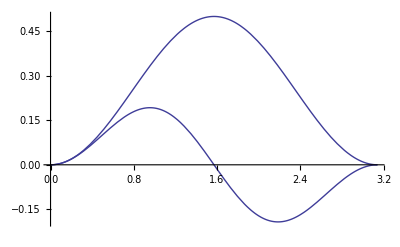

```mathematica
Plot[intlgnd/.n->{1,2},{theta,0,Pi}]
```

verify

```mathematica
D[intlgnd,theta] == Sin[theta] LegendreP[n,Cos[theta]]// FullSimplify
```

True

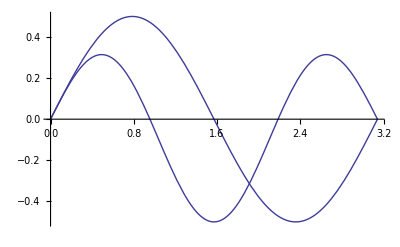

```mathematica
Plot[Sin[theta] LegendreP[n,Cos[theta]]/. n->{1,2},{theta,0,Pi}]
```

```mathematica
Limit[falpha[a,s,u] , h->Infinity]
```

DirectedInfinity[-s BesselJ[1/2+n,s u] BesselY[1/2+n,a u]+s BesselJ[1/2+n,a u] BesselY[1/2+n,s u]]

Special case; r0 == sigma

```mathematica
solnBJY /. r0 -> s // FullSimplify
```

((1+2 n) π s u^3 (-BesselJ[3/2+n,s u] BesselY[1/2+n,s u]+BesselJ[1/2+n,s u] BesselY[3/2+n,s u]) (((n-h s) BesselJ[1/2+n,s u]-s u BesselJ[3/2+n,s u]) BesselY[1/2+n,r u]+BesselJ[1/2+n,r u] ((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])))/(8 √(r s) (n+n^2-s (h+h^2 s+s u^2)+(((-n+h s) BesselJ[1/2+n,s u]+s u BesselJ[3/2+n,s u])^2+((-n+h s) BesselY[1/2+n,s u]+s u BesselY[3/2+n,s u])^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)))

```mathematica
Limit[solnBJY/. n->0,s->0]  //Simplify
```

(Sin[r u] Sin[r0 u])/(2 a π r r0)

((1+2 n) π u^2 (-n BesselJ[1/2+n,r u] BesselY[1/2+n,0]+n BesselJ[1/2+n,0] BesselY[1/2+n,r u]) (-n BesselJ[1/2+n,r0 u] BesselY[1/2+n,0]+n BesselJ[1/2+n,0] BesselY[1/2+n,r0 u]))/(8 √r √r0 (n+n^2+(n^2 BesselJ[1/2+n,0]^2+n^2 BesselY[1/2+n,0]^2)/(BesselJ[1/2+n,a u]^2+BesselY[1/2+n,a u]^2)))